## Pi2 Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=(10#1+#2)&@@@Partition[RealDigits[Pi,10,20001][[1,2;;]],2];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[series]
```

{0.145877,0.962094}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|1→1,10→258,3→2065,12→162,8→325,9→300,13→130,19→33,6→697,5→1043,2→2215,4→1561,16→70,17→63,33→7,11→178,27→6,23→17,7→498,22→22,14→104,18→44,21→31,26→9,38→2,36→4,15→79,20→18,25→15,28→6,48→1,37→3,32→4,44→1,24→11,29→5,31→2,30→4,39→1,47→1,43→1,34→1,35→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

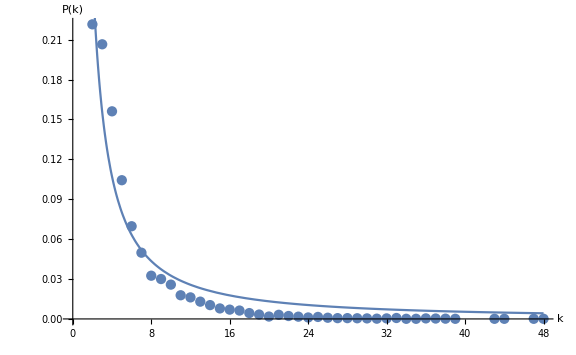
{{C→0.648613,γ→1.29927},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|1→1,5→881,3→2168,9→205,8→286,10→154,2→3619,4→1363,7→450,6→600,16→16,19→4,13→40,12→61,11→96,15→18,23→1,26→1,18→3,17→6,14→23,20→2,22→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

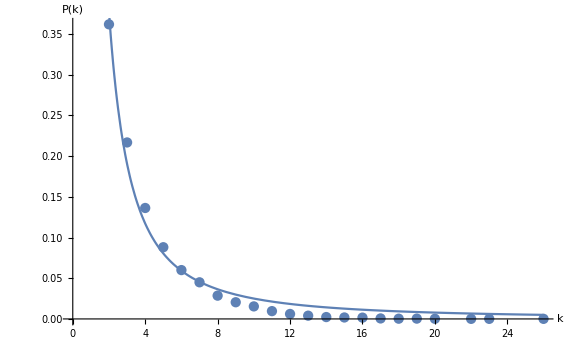
{{C→1.21148,γ→1.68494},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```